#### define variables

```mathematica
xc = 1;
yc = 0;
npts = 10;
ri = 1;
kg = 1.1;
minDist=0;
sunnyshady = Sin[0.3x]Sin[0.5y];
d=rg-(ri+minDist);
rg = ri *kg;
ptc = {xc,yc};
initialCircle = Circle[ptc,ri];
initialCirclePoints=CirclePoints[ptc,ri,npts];
```

#### define functions to use

```mathematica
funcSunnyShady[x_,y_]:=Sin[.3x]Sin[.5y]
```

```mathematica
findGradPoints[scalarFunc_,circlePoints_,x_,y_]:=Module[{gradFunc,listGradPoints},
gradFunc=Grad[scalarFunc[x,y],{x,y}];
listGradPoints=gradFunc/.{x->circlePoints[[All,1]],y->circlePoints[[All,2]]};
Transpose[listGradPoints]
]
```

findGradPoints is now a transpose so it yields a list like {{x1,y1},{x2,y2},...,{xn,yn}} rather than {{x1,x1,...,xn},{y1,y2,...,yn}}
Also look at this pretty module thing. You can define things locally in just this function and then make it so much more readable. Woo, Mathematica! Also Jared. Thanks, Jared.

```mathematica
findMaxPoint[listCirclePoints_,listGradPoints_]:=Module[{listNorms,maxPosition,listMaxPoints,listMaxGradPoints,betterListMaxGradPoints},
listNorms=Norm/@listGradPoints;
maxPosition=Position[listNorms,Max[listNorms]];
listMaxGradPoints=listCirclePoints[[#]]&/@maxPosition;
Flatten[RandomChoice[listMaxGradPoints]]
]
```

So, findMaxPoint. This is a thing.
listNorms is a list of magnitudes from the list of points.
maxPosition is a list of the position(s) in the list that have the greatest gradient value.
listMaxPoints returns a list of the coordinates of points on the circle with the greatest gradient value.
then we randomly choose one of the points (sometimes, there are more than one) and flattens it (so it looks like {x1,y1})

```mathematica
findNewCenter[ptc_,ptn_,d_]:=Module[{v, vhat},
v=ptn-ptc;
vhat=Norm[v];
vhat d + ptc
]
```

v is the vector in the direction of the line segment between the initial circle center and the max grad point
vhat is that in unit vector form
vhat * d makes it the length we want, add it to ptc to get the offset, woo new center!

#### find the point on boundary of circle with maximum gradient and the new center point

```mathematica
listPoints=findGradPoints[funcSunnyShady,initialCirclePoints,x,y];
```

```mathematica
p=findMaxPoint[initialCirclePoints,listPoints]
```

{2,0}

#### draw things

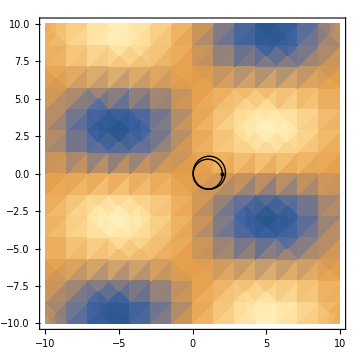

```mathematica
p0 = DensityPlot[sunnyshady,{x,-10,10},{y,-10,10}];
p1 = Graphics[initialCircle];
p2=Graphics[Point[p]];
p3=Graphics[Circle[ptnew,rg]];
Show[p0,p1,p2,p3,ImageSize->Medium]
```